# Introduction to Lists

Math 213 - Math with Mathematica
Christopher Hanusa

## Aim

In Mathematica, the key data structure is the list.  Whenever multiple numbers are to be grouped together into one object, this object will be a list.  For example, if you wish to reference the point (2,1) in the (x,y) plane, you would use write it as the list {2,1}.  Every list is surrounded by a left brace { and a right brace }.  Entries of the list are separated by commas.

The aim of this tutorial is to introduce the user to lists, highlight important commands which generate lists, and show multiple ways to present lists in digestible formats.

These tutorials are meant to be interactive.  You should be playing around with the inputs to try to see what changes in the output when you change the inputs. Before progressing onto the next part of the tutorial, make sure to complete the Comprehension Question sections, working with your classmates.

Throughout this and future tutorials, it is important to pay attention to the syntax of the commands.  What inputs are inside the left bracket [ and the right bracket ]?  (How many inputs?  What does each input tell Mathematica to do?) What is the output of the command? (Does it give a list? a graphics object?)  You will know that you have mastered the command if you can create working Mathematica code involving the command AND you can explain what the command does in sentences.

## The Range command

We first start by creating simple lists of integers using the Range command.  
A Range command has between 1 and 3 inputs; more inputs allow for more complex behavior.  Compare the following inputs and outputs.

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[2,10]
```

{2,3,4,5,6,7,8,9,10}

```mathematica
Range[0,10,2]
```

{0,2,4,6,8,10}

When there is only one input n, the output will be a list of integers starting at 1 and increasing to n.
When there are two inputs m and n, the output will be the list of integers starting at m and increasing to n.
When there are three inputs m, n, and incr, then the output will be the list of integers starting at m and increasing to n in increments of incr.

## Comprehension Questions:

### 1. What do you think will happen if the input to Range is a negative integer? A non-integer? Try it out right here! Write a sentence about each to explain what you learned. (To write a sentence, create a new text cell by clicking below this cell when the cursor turns horizontal and typing Option-7, or right clicking and navigating to Insert New Cell > Text.)

### 2. For each of the following Range commands, complete the following sub-questions. (a) BEFORE EVALUATING THE COMMAND, what list do you expect the command to give? Or do you expect an error? (b) Now, evaluate the command. Did it do what you expect it to do? (c) If not, figure out what went wrong with your reasoning.

```mathematica
Range[1]
```

```mathematica
Range[Pi]
```

```mathematica
Range[10,5]
```

```mathematica
Range[3,4,1/5]
```

```mathematica
Range[10,30,Pi]
```

```mathematica
Range[Pi,30,10]
```

```mathematica
Range[100,0,-8]
```

### 3. Determine which Range commands give the following lists.

```mathematica
{1,2,3,4,5,6}
```

```mathematica
{-5,-4,-3,-2}
```

```mathematica
{1,3,5,7,9,11}
```

```mathematica
{1.,1.5,2.,2.5,3.,3.5,4.,4.5}
```

```mathematica
{17,27,37,47,57,67,77,87,97}
```

```mathematica
{-1,-2,-3,-4,-5}
```

#### Possible Solutions

```mathematica
Range[6]
```

```mathematica
Range[-5,-2]
```

```mathematica
Range[1,11,2]
```

```mathematica
Range[1,4.5,.5]
```

```mathematica
Range[17,100,10]
```

```mathematica
Range[-1,-5,-1]
```

## The Table command, Part 1

The most important command to master at this early stage is the Table command.  This command will generate a list based on a function you specify.  
First, let's analyze the structure of a Table command:

```mathematica
Table[x^2,{x,0,5}]
```

{0,1,4,9,16,25}

There are always two inputs, a function (x^2) and a list ({x,0,5}) that specifies the values of x that will be inserted into the function. 
The first element in the list is always the variable that is modified by the function (in this case, x).  
	[Notice that the variable is automatically colored green in this list and in the function for your convenience.]
Depending on what the list contains, the values of this variable are specified in different ways, using the same type of syntax as in the Range command above.
If the list is of length two, such as {x,5}, then the values of x that will be inserted are between 1 and that value (5).

```mathematica
Table[x^2,{x,5}]
```

{1,4,9,16,25}

If the list is of length three, such as {x,-1,5}, then the values of x that will be inserted are from the first number to the second number.

```mathematica
Table[x^2,{x,-1,5}]
```

{1,0,1,4,9,16,25}

If the list is of length four, such as {x,0,10,2}, then the values of x that will be inserted are from the first number to the second number by increments of the last number.

```mathematica
Table[x^2,{x,0,10,2}]
```

{0,4,16,36,64,100}

There is one NEW type of allowed syntax.
If the list is contains a variable and another nested list, such as {x,{0,10,2}}, then the values of x that will be inserted are exactly the values in this nested list, output in that order.

```mathematica
Table[x^2,{x,{0,10,2}}]
```

{0,100,4}

## Comprehension Questions:

### 4. For each of the following Table commands, complete the following sub-questions. (a) BEFORE EVALUATING THE COMMAND, what list do you expect the command to give? Or do you expect an error? (b) Now, evaluate the command. Did it do what you expect it to do? (c) If not, figure out what went wrong with your reasoning.

```mathematica
Table[i,{i,10}]
```

```mathematica
Table[y^2,{x,5}]
```

```mathematica
Table[i,{2,6}]
```

```mathematica
Table[x^2,{x,Pi,10}]
```

```mathematica
Table[-z,{z,1.5,3.5,0.5}]
```

```mathematica
Table[a,{a,1,10,Pi}]
```

```mathematica
Table[Sqrt[b],{b,{1,10,Pi}}]
```

```mathematica
Table[{x,x^2},{x,3,6}]
```

```mathematica
Table[Range[i],{i,1,5}]
```

Discuss these answers with your neighbors.

### 5. Determine which Table commands give the following lists. There are multiple solutions for each one.

```mathematica
{2 π,2+2 π,4+2 π,6+2 π,8+2 π}
```

```mathematica
{1,8,27,64,125,216}
```

```mathematica
{1/4,1/5,1/6,1/7}
```

```mathematica
{2,1,0,1,2,3}
```

```mathematica
{1/10,1/2,-1/4}
```

```mathematica
{{0,0,0},{0,0,1},{0,0,2},{0,0,3},{0,0,4}}
```

```mathematica
{{-3,9},{-2,4},{-1,1},{0,0}}
```

#### Solutions

```mathematica
Table[2(Pi+i),{i,0,4}]
```

```mathematica
Table[i^3,{i,6}]
```

```mathematica
Table[1/i,{i,4,7}]
```

```mathematica
Table[Abs[i],{i,-2,3}]
```

```mathematica
Table[1/i,{i,{10,2,-4}}]
```

```mathematica
Table[{0,0,i},{i,0,4}]
```

```mathematica
Table[{i,i^2},{i,-3,0,1}]
```

## Challenge Questions

### 6. Give a Range or Table command to give the following lists.

```mathematica
{π/2,(3 π)/2,(5 π)/2,(7 π)/2,(9 π)/2,(11 π)/2}
```

```mathematica
{{0,1,2},{1,3,4},{2,6,8},{3,10,16},{4,15,32}}
```

```mathematica
{ab+1,-ab+4,ab+9,-ab+16,ab+25}
```

## Output Form of Lists

There are two commands that will help you to take a list and present it in an more appealing way.

### The TableForm command

The TableForm command will take a list (or list of lists) and display them in a tabular environment, which is sometimes convenient when you want to line up your data for easier reading and comparing.

```mathematica
TableForm[{{1,2,3},{2,4,6},{3,6,9}}]
```

1 | 2 | 3
2 | 4 | 6
3 | 6 | 9

```mathematica
squares=Table[{i,i^2},{i,1,10}]
TableForm[squares]
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

1 | 1
2 | 4
3 | 9
4 | 16
5 | 25
6 | 36
7 | 49
8 | 64
9 | 81
10 | 100

### The TraditionalForm command

Another output form is traditional form, which tries to take the output and make it look the most like a person might write it.  For example. TraditionalForm takes two dimensional lists and outputs them as matrices.

```mathematica
TraditionalForm[{{1,2,3},{2,4,6},{3,6,9}}]
```

(1 | 2 | 3
2 | 4 | 6
3 | 6 | 9)

I find TraditionalForm the most helpful for displaying polynomials.  Look at how the Taylor Series polynomial approximation looks in the default form, and how it looks in Traditional Form.

```mathematica
series=Normal[Series[1/(1-x-x^2),{x,0,10}]]
```

1+x+2 x^2+3 x^3+5 x^4+8 x^5+13 x^6+21 x^7+34 x^8+55 x^9+89 x^10

```mathematica
TraditionalForm[series]
```

89 x^10+55 x^9+34 x^8+21 x^7+13 x^6+8 x^5+5 x^4+3 x^3+2 x^2+x+1

## Visual display of lists

### The ListPlot and ListLinePlot commands

If your list contains a sequence of data, you can use the ListPlot function to generate a scatterplot, where if s_i is sequence entry i, then it is plotted at coordinates (i,s_i).

{1,3,4,6,2,7,8}

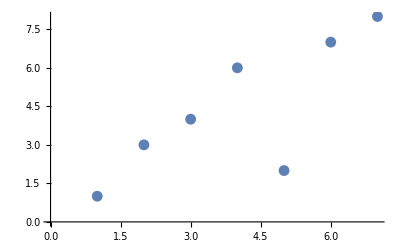

```mathematica
data1={1,3,4,6,2,7,8}
ListPlot[data1]
```

If you prefer that your points are connected (perhaps to better see a trend), then instead use ListLinePlot.

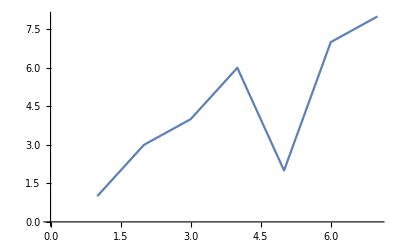

```mathematica
ListLinePlot[data1]
```

You may instead have a set of data that is a list of x-y coordinate pairs (each pair is a list of two elements), and ListPlot and ListLinePlot can handle these as well.

```mathematica
data2={{0,0},{0,-1},{-1,1},{1,2},{2,-3},{-3,-5},{-5,8},{8,13}}
```

{{0,0},{0,-1},{-1,1},{1,2},{2,-3},{-3,-5},{-5,8},{8,13}}

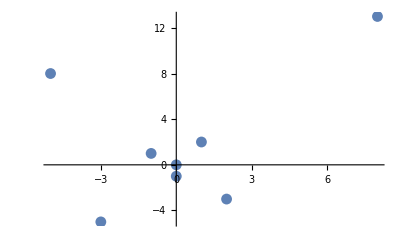

```mathematica
ListPlot[data2]
```

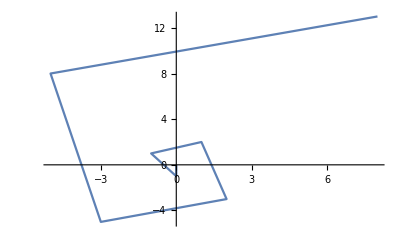

```mathematica
ListLinePlot[data2]
```

### The Tally and Histogram commands

Here we simulate rolling a six-sided die 200 times.

```mathematica
dice=RandomInteger[{1,6},200]
```

{2,6,2,2,5,5,2,1,3,5,4,2,4,1,5,5,5,3,4,2,2,2,6,3,5,1,1,4,6,3,6,3,1,1,3,5,2,6,4,5,2,3,1,1,1,2,2,5,5,3,5,3,6,2,3,3,1,2,4,2,4,4,4,3,2,3,5,2,1,6,2,1,6,1,1,3,2,3,4,3,4,4,1,6,1,5,3,2,2,3,4,4,5,2,5,5,3,6,2,4,1,1,2,2,3,4,3,4,6,6,4,1,1,4,3,3,3,3,5,2,6,4,5,4,1,3,1,4,6,3,3,5,4,5,3,2,4,5,4,2,1,4,2,3,6,4,2,6,2,4,1,3,5,1,1,2,1,3,1,5,2,6,5,2,4,4,5,6,3,5,4,3,6,5,4,2,1,6,4,6,3,2,3,3,3,3,4,2,4,4,1,4,5,6,5,1,4,3,3,4}

We can take the data and tally how many of each output arise using the Tally command

```mathematica
Tally[dice]
```

{{2,37},{6,22},{5,30},{1,31},{3,41},{4,39}}

We should probably Sort the entries and then use TableForm so that it is easier to read

```mathematica
TableForm[Sort[Tally[dice]]]
```

1 | 31
2 | 37
3 | 41
4 | 39
5 | 30
6 | 22

Or we can represent the data visually by way of the Histogram command

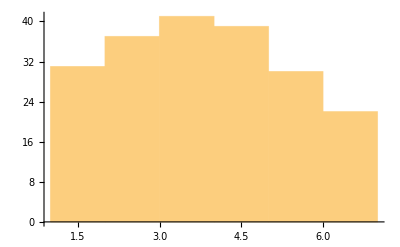

```mathematica
Histogram[dice]
```

## Comprehension Questions

### 7. Suppose you wanted a visual representation of the rolls of the 200 dice, but chronologically instead of grouped together. How could you present this? Should the data points be connected or not? Why or why not?

## Useful list commands

### Length

Length will tell you how many elements there are in the list.

```mathematica
Length[{1,2,3}]
```

3

```mathematica
Length[{1,{2,3}}]
```

2

### Total

Total will sum the values in the list.

```mathematica
Total[{1,2,3}]
```

6

```mathematica
powersOfTen=Table[10^i,{i,0,5}]
```

{1,10,100,1000,10000,100000}

```mathematica
Total[powersOfTen]
```

111111

## Comprehension Questions:

### 8. For each of the following commands, complete the following sub-questions. (a) What list do you expect the command to give? Or do you expect an error? (b) Now evaluate the command. Did it do what you expect it to do? (c) If not, figure out what went wrong with your reasoning.

```mathematica
Length[{1,2,3,4}]
```

```mathematica
Length[{{1,2,3}}]
```

```mathematica
Total[{1,2,3,4}]
```

```mathematica
Total[{{1,2},{3,4}}]
```

```mathematica
Total[{{1,2,3}}]
```

Discuss these answers with your neighbors.

## Exploration Questions:

### 9. There are many statistics that Mathematica can access about lists. Take some time to learn about Mean, Median, and about the related commands that are at the bottom of those pages.

## Challenge Question:

### 10. How could you use the commands from Question 9 to find the midpoint of a line with the following coordinates?

```mathematica
{{0,0},{2,3}}
```